```mathematica
Datuzzi= Import["C:\\Users\\lucia\\Desktop\\Unime\\Tesi\\TableM2.txt","Table"];
Omega
```

Omega

Drop::normal: Nonatomic expression expected at position 1 in Drop[Table, 0].

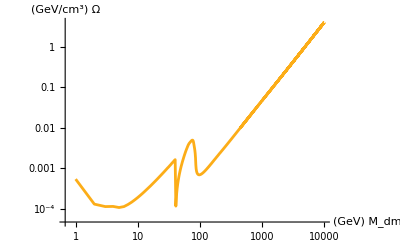

```mathematica
ListLogLogPlot[Table[{Datuzzi[[i,2]],Datuzzi[[i,1]]},{i,1,Dimensions[Datuzzi][[1]]}],Joined->True, ColorFunction->"SolarColors", AxesLabel->{ Subscript[M, dm] "(GeV)" ,Ω  "(GeV/cm^3)"}]
```